```mathematica
ClearAll["Global`*"]

(* Lithium Niobaote *)
d={{0,0,0,0,d31,-d22},{-d22,d22,0,d31,0,0},{d31,d31,d33,0,0,0}};
dvalues = {d31-> -4.3*10^-12,d33->-27*10^-12,d22->2.1*10^-12} (*m/V*);

β={{β11,0,0},{0,β11,0},{0,0,β33}};
βvalues = {β11-> 1/(2.21*2.21),β33->1/(2.13*2.13)} ;
nvalues={no-> 2.21, ne->2.13};

d//MatrixForm
β//MatrixForm

(((2*d33)/ne^4)/((2*d33)/ne^4))/.βvalues/.nvalues/.dvalues//N
```

(0 | 0 | 0 | 0 | d31 | -d22
-d22 | d22 | 0 | d31 | 0 | 0
d31 | d31 | d33 | 0 | 0 | 0)

(β11 | 0 | 0
0 | β11 | 0
0 | 0 | β33)

1.

```mathematica
Dvec[x_,y_,z_]:={Dx[x,y,z],Dy[x,y,z],Dz[x,y,z]};

Fromχ1tod1={χ[1,1,1]-> 2*d[[1,1]],χ[1,1,2]-> 2*d[[1,6]],χ[1,1,3]-> 2*d[[1,5]],χ[1,2,1]-> 2*d[[1,6]],χ[1,2,2]-> 2*d[[1,2]],χ[1,2,3]-> 2*d[[1,4]],χ[1,3,1]-> 2*d[[1,5]],χ[1,3,2]-> 2*d[[1,4]],χ[1,3,3]-> 2*d[[1,3]]};
Fromχ2tod2={χ[2,1,1]-> 2*d[[2,1]],χ[2,1,2]-> 2*d[[2,6]],χ[2,1,3]-> 2*d[[2,5]],χ[2,2,1]-> 2*d[[2,6]],χ[2,2,2]-> 2*d[[2,2]],χ[2,2,3]-> 2*d[[2,4]],χ[2,3,1]-> 2*d[[2,5]],χ[2,3,2]-> 2*d[[2,4]],χ[2,3,3]-> 2*d[[2,3]]};
Fromχ3tod3={χ[3,1,1]-> 2*d[[3,1]],χ[3,1,2]-> 2*d[[3,6]],χ[3,1,3]-> 2*d[[3,5]],χ[3,2,1]-> 2*d[[3,6]],χ[3,2,2]-> 2*d[[3,2]],χ[3,2,3]-> 2*d[[3,4]],χ[3,3,1]-> 2*d[[3,5]],χ[3,3,2]-> 2*d[[3,4]],χ[3,3,3]-> 2*d[[3,3]]};

Γ[i_,l_,m_]:=Sum[Sum[(χ[i,j,k]/ϵ0)*β[[j,l]]*β[[k,m]],{j,1,3}],{k,1,3}];
P2i[i_,x_,y_,z_]:=Sum[Sum[Γ[i,l,m]*Dvec[x,y,z][[l]]*Dvec[x,y,z][[m]],{l,1,3}],{m,1,3}];
```

```mathematica
P2[x_,y_,z_]:=Table[P2i[i,x,y,z],{i,1,3}]/.Fromχ1tod1/.Fromχ2tod2/.Fromχ3tod3//Simplify;
P2[x,y,z]//Simplify//Expand//MatrixForm
```

(-(4 d22 β11^2 Dx[x,y,z] Dy[x,y,z])/ϵ0+(4 d31 β11 β33 Dx[x,y,z] Dz[x,y,z])/ϵ0
-(2 d22 β11^2 Dx[x,y,z]^2)/ϵ0+(2 d22 β11^2 Dy[x,y,z]^2)/ϵ0+(4 d31 β11 β33 Dy[x,y,z] Dz[x,y,z])/ϵ0
(2 d31 β11^2 Dx[x,y,z]^2)/ϵ0+(2 d31 β11^2 Dy[x,y,z]^2)/ϵ0+(2 d33 β33^2 Dz[x,y,z]^2)/ϵ0)

```mathematica
TNBbasisZCUT={Dx[x,y,z]-> -DTE*Sin[ϕ],Dy[x,y,z]-> DTE*Cos[ϕ],Dz[x,y,z]-> DTM};
TNBbasisXCUT={Dx[x,y,z]-> DTM,Dy[x,y,z]-> -DTE*Sin[ϕ],Dz[x,y,z]-> DTE*Cos[ϕ]};
TNBbasis =TNBbasisZCUT;

rules={Sin[ϕ]^2->FourierCosSeries[Sin[ϕ]^2,ϕ,5],
Sin[ϕ]^3->FourierSinSeries[Sin[ϕ]^3,ϕ,5],
Cos[ϕ]^2->FourierCosSeries[Cos[ϕ]^2,ϕ,5],
Cos[ϕ]^3->FourierCosSeries[Cos[ϕ]^3,ϕ,5]};

P2eff[x_,y_,z_]:=P2[x,y,z]/.TNBbasis/.{ϵ0->1,DTE->1,DTM->0}//FullSimplify//Expand;
P2eff[x,y,z]/.rules//Expand//MatrixForm
```

(4 d22 β11^2 Cos[ϕ] Sin[ϕ]
2 d22 β11^2 Cos[2 ϕ]
2 d31 β11^2)

```mathematica
TvecZCUT={Cos[ϕ],Sin[ϕ],0};
NvecZCUT={-Sin[ϕ],Cos[ϕ],0};
BvecZCUT={0,0,1};

TvecXCUT={0,Cos[ϕ],Sin[ϕ]};
NvecXCUT={0,-Sin[ϕ],Cos[ϕ]};
BvecXCUT={1,0,0};

vec=P2eff[x,y,z]/.rules//Expand;

TNBruleZ=Solve[vec==TT*TvecZCUT+NN*NvecZCUT+BB*BvecZCUT,{TT,NN,BB}][[1]]//FullSimplify//Expand;
TNBruleX=Solve[vec==TT*TvecXCUT+NN*NvecXCUT+BB*BvecXCUT,{TT,NN,BB}][[1]]//FullSimplify//Expand;
TNBrule=TNBruleZ;
TNBrule
```

{TT→2 d22 β11^2 Sin[3 ϕ],NN→2 d22 β11^2 Cos[3 ϕ],BB→2 d31 β11^2}

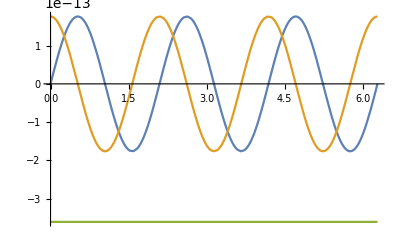

```mathematica
{PT,PN,PB}={TT,NN,BB}/.TNBrule;
{PTvalue,PNvalue,PBvalue}={PT,PN,PB}/.dvalues/.βvalues;

Plot[{PTvalue,PNvalue,PBvalue},{ϕ,0,2π},PlotRange->All]
```

```mathematica
kp=7.2420*10^6;
ks=1.4378*10^7;
δk=2*kp-ks;
δk=1400000
```

1400000

```mathematica
P2Target=PNvalue/MaxValue[PNvalue,ϕ];
Λ=(2*π)/δk;
ds=30*10^-9;
a=0.2;
F[s_]:=-a*Cos[δk*s];
(*-----------------------*)

(* Finding the curve γ *)
ϕvec={};
svec={0};
xvec={0};
yvec={0};
ϕguess=0.01;

For[s=0,s<=Λ,s=s+ds,
ϕroot=FindRoot[P2Target-F[s],{ϕ,ϕguess},PrecisionGoal->1000][[1]][[2]];
ϕvec=Append[ϕvec,ϕroot];
ϕguess=ϕroot;
svec=Append[svec,s];
xvec=Append[xvec,xvec[[-1]]+ds*Cos[ϕroot]];
yvec=Append[yvec,yvec[[-1]]+ds*Sin[ϕroot]]]
ϕvec=Append[ϕvec,ϕvec[[1]]];
xvec=xvec-Min[xvec];
yvec=yvec-Min[yvec];
γ=Transpose[{xvec,yvec}];
(*-----------------------*)

(* Finding the curvature κ of the curve γ*)
domain=Table[t,{t,1,Length[svec],1}];

xinterp=Interpolation[xvec];
yinterp=Interpolation[yvec];

dxinterp=xinterp';
dyinterp=yinterp';

ddxinterp=xinterp'';
ddyinterp=yinterp'';

κ=((dxinterp[domain]*ddyinterp[domain])-(dyinterp[domain]*ddxinterp[domain]))/((dxinterp[domain]*dxinterp[domain])+(dyinterp[domain]*dyinterp[domain]))^(3/2);
(*-----------------------*)
```

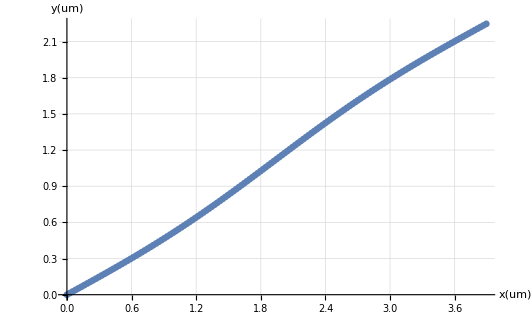

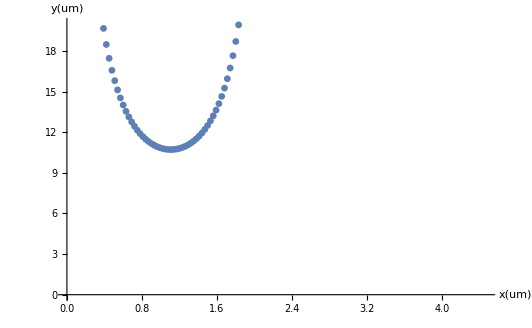

```mathematica
ListPlot[γ*10^6,GridLines->Automatic,AxesLabel->{x[um],y[um]},AxesStyle->Directive[White, 15]]
ListPlot[Transpose[{svec*10^6,10^6/κ}],PlotRange->{0,20},AxesLabel->{x[um],y[um]},AxesStyle->Directive[White, 15]]
```

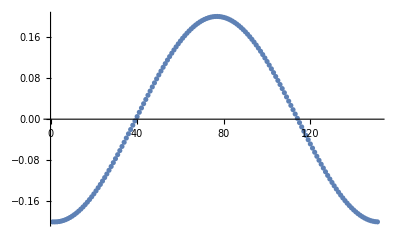
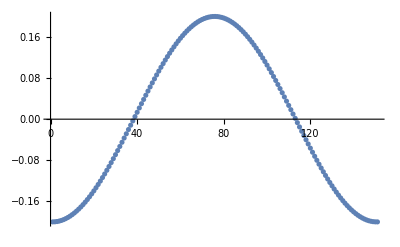

```mathematica
{ListPlot[F[svec]],ListPlot[P2Target/.{ϕ->ϕvec}]}
```

```mathematica
SetDirectory["C:\\Users\\conde\\Desktop"]
Export["Anisotropy-Assisted-QPM_Z-cut_TE-TE_.dat",γ]
```

C:\Users\conde\Desktop

Anisotropy-Assisted-QPM_Z-cut_TE-TE_.dat

```mathematica
IntegerPart[Table[i,{i,1.3*10^6,1.5*10^6,0.025*10^6}]]
```

{1300000,1325000,1350000,1375000,1400000,1425000,1450000,1475000,1500000}

```mathematica
SetDirectory["C:\\Users\\conde\\Desktop"];
δkvec=IntegerPart[Table[i,{i,1.3*10^6,1.5*10^6,0.025*10^6}]];
w=750; (*in [nm]*)
a=0.25;
savingorder={a5,b5,c5,d5,e5,f5,g5,h5,i5};
ds=25*10^-9;
(*-----------------------*)

For[i=1,i<=Length[δkvec],i++,
Λ=(2*π)/δkvec[[i]]//N;
ϕvec={};
svec={};
xvec={0};
yvec={0};
ϕguess=0.01;
F[s_]:=-a*Cos[δkvec[[i]]*s];
For[s=0,s<=Λ,s=s+ds,
svec=Append[svec,s];
ϕroot=FindRoot[P2Target-F[s],{ϕ,ϕguess},PrecisionGoal->1000][[1]][[2]];
ϕvec=Append[ϕvec,ϕroot];
ϕguess=ϕroot;
xvec=Append[xvec,xvec[[-1]]+ds*Cos[ϕroot]];
yvec=Append[yvec,yvec[[-1]]+ds*Sin[ϕroot]]
];
xvec=xvec-Min[xvec];
yvec=yvec-Min[yvec];
xvec=Insert[xvec,"x",1];
yvec=Insert[yvec,"y",1];
γ=Transpose[{xvec,yvec}];
Export[ToString[savingorder[[i]]]<>"_Anisotropy-Assisted-QPM_Z-cut_t400nm_dk="<>ToString[δkvec[[i]]]<>"rad-m_w="<>ToString[w]<>"nm_Lambda="<>ToString[Λ*10^6]<>"um_ds="<>ToString[ds*10^9]<>"nm_a="<>ToString[a]<>".dat",γ]
]
```